```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNTau"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
runst=16;
runend=39;
Print["Runs in the list: ",runNum=descdat[[runst;;runend,4]]];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis\mNTau

(DescDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Runs in the list: {13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142}

Size: 24

FittedModel[0.0781624 ⅇ^(-0.0136955 t)+0.0506828 ⅇ^(-0.00356783 t)]

Sigmas: {0.000778321,-0.000586769,-0.000537916,-0.000493507,-0.0000875389,0.000486196,0.000381461,0.000145503,0.000528476,-0.000810426,-0.000257736,0.000437418,0.000314056,0.000392068,0.000529178,0.000199689,-0.000346323,-0.0000192096,-0.000287998,-0.0000814235,0.000234531,-0.000475804,-0.000580055,-0.000574544,0.000025692,-0.00023663,0.000293824,0.000232021,0.0000195941,0.000251876,0.0000877107,-0.0000688093,0.000140271,0.000226698,0.00021633,0.000195958,0.000118027}

Chi^2/ndf: 1.50312×10^-7

| DF | SS | MS
Model | 4 | 0.0257323 | 0.00643308
Error | 33 | 2.63709×10^-6 | 7.99118×10^-8
Uncorrected Total | 37 | 0.0257349 | 
Corrected Total | 36 | 0.0115161 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0781624 | 0.00148857 | 52.5085 | 2.21038×10^-33
cc | -0.0136955 | 0.00051798 | -26.4402 | 8.69068×10^-24
dd | 0.0506828 | 0.00199602 | 25.3919 | 3.10781×10^-23
ee | -0.00356783 | 0.0000861147 | -41.4312 | 4.90358×10^-30

AdjustedRSquared | 0.999885
AIC | -485.147
BIC | -477.093
RSquared | 0.999898

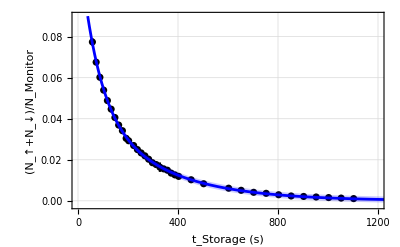

```mathematica
finpt=ReadList["expsuperdat4-Cu.dat",{Real,Real,Real}];
finftpt=Table[{finpt[[k]][[1]],finpt[[k]][[2]]},{k,1,Dimensions[finpt][[1]]}];
finrealpt=Table[{{finpt[[k]][[1]],2*.397183},{finpt[[k]][[2]],finpt[[k]][[3]]}},{k,1,Dimensions[finpt][[1]]}];
errallseries=Sqrt[finpt[[;;,3]]^2+(2*.397183)^2];
Print[nlm3=NonlinearModelFit[finftpt,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t,Weights->errallseries]];
Print["Sigmas: ",(nlm3["FitResiduals"]/errallseries)];
Print["Chi^2/ndf: ",Total[((nlm3["FitResiduals"]/errallseries))^2]/(Dimensions[finpt][[1]]-2)];
nlm3["ANOVATable"]
nlm3["ParameterTable"]
Grid[Transpose[{#,nlm3[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[finrealpt,PlotRange->{{0,1200},{-.002,.09}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1400}],
Plot[{nlm3[xx],nlm3[xx]+nlm3["ParameterErrors"][[1]],nlm3[xx]-nlm3["ParameterErrors"][[1]]},{xx,0,1300},Filling->{2->{3}},PlotRange->{{0,1200},{-.002,.09}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
(***)
```

```mathematica
stime=nlm3["ParameterTable"][[1]][[1]][[3]][[2;;3]];
ltime=nlm3["ParameterTable"][[1]][[1]][[5]][[2;;3]];
Print["Short decay time (s): ", N[1/PlusMinus[stime[[1]],stime[[2]]]],"\n",
"Long decay time (s): ",N[-1/PlusMinus[ltime[[1]],ltime[[2]]]]]
Print["If t1/2 is removed from the above:"]
Print["Short decay time (s): ", N[1/(-PlusMinus[stime[[1]],stime[[2]]]-(1/PlusMinus[880,1]))],"\n",
"Long decay time (s): ",N[1/(-PlusMinus[ltime[[1]],ltime[[2]]]-(1/PlusMinus[880,1]))]]
```

Short decay time (s): -73.±2.8
Long decay time (s): 280.3±6.8

If t1/2 is removed from the above:

Short decay time (s): 79.6±3.3
Long decay time (s): 411.±15.

FittedModel[77.6556 ⅇ^(0.00341948 t)+79.362 ⅇ^(0.00341948 t)]

Sigmas: {-8.18967,-6.81487,-5.67357,-6.04515,-2.85108,1.66535,0.163434,13.2681,-60.1717,-0.850163,79.9423,2.17922,-2.13341,2.09933,12.5878,1.11117,2.12198,-5.24884,-22.0361,0.281864}

Chi^2/ndf: 316.356

| DF | SS | MS
Model | 4 | 2.5391×10^6 | 634776.
Error | 16 | 6986.92 | 436.682
Uncorrected Total | 20 | 2.54609×10^6 | 
Corrected Total | 19 | 210984. |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 77.6556 | 8.96528 | 8.66182 | 1.94829×10^-7
cc | 0.00341948 | 630271. | 5.42541×10^-9 | 1
dd | 79.362 | 8.96531 | 8.85212 | 1.45644×10^-7
ee | 0.00341948 | 616719. | 5.54463×10^-9 | 1

AdjustedRSquared | 0.99657
AIC | 184.342
BIC | 189.32
RSquared | 0.997256

FittedModel[113.835 ⅇ^(-0.00770424 t)+115.436 ⅇ^(0.00687298 t)]

Sigmas: {6.75619,7.84603,13.9139,21.4557,15.4439,40.3462,-122.871,-5.395,223.737,-15.8208,-38.629,-35.5488,-5.86456,-53.7446,-50.9681,-80.1585,-154.576,-0.0606008,91.7577,106.07}

Chi^2/ndf: 3609.38

| DF | SS | MS
Model | 4 | 1.48789×10^7 | 3.71972×10^6
Error | 16 | 79715.6 | 4982.22
Uncorrected Total | 20 | 1.49586×10^7 | 
Corrected Total | 19 | 3.4914×10^6 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 113.835 | 479.158 | 0.237573 | 0.815227
cc | -0.00770424 | 0.0511269 | -0.150688 | 0.882105
dd | 115.436 | 68.5834 | 1.68314 | 0.111754
ee | 0.00687298 | 0.00144979 | 4.74067 | 0.000221609

AdjustedRSquared | 0.993339
AIC | 233.03
BIC | 238.009
RSquared | 0.994671

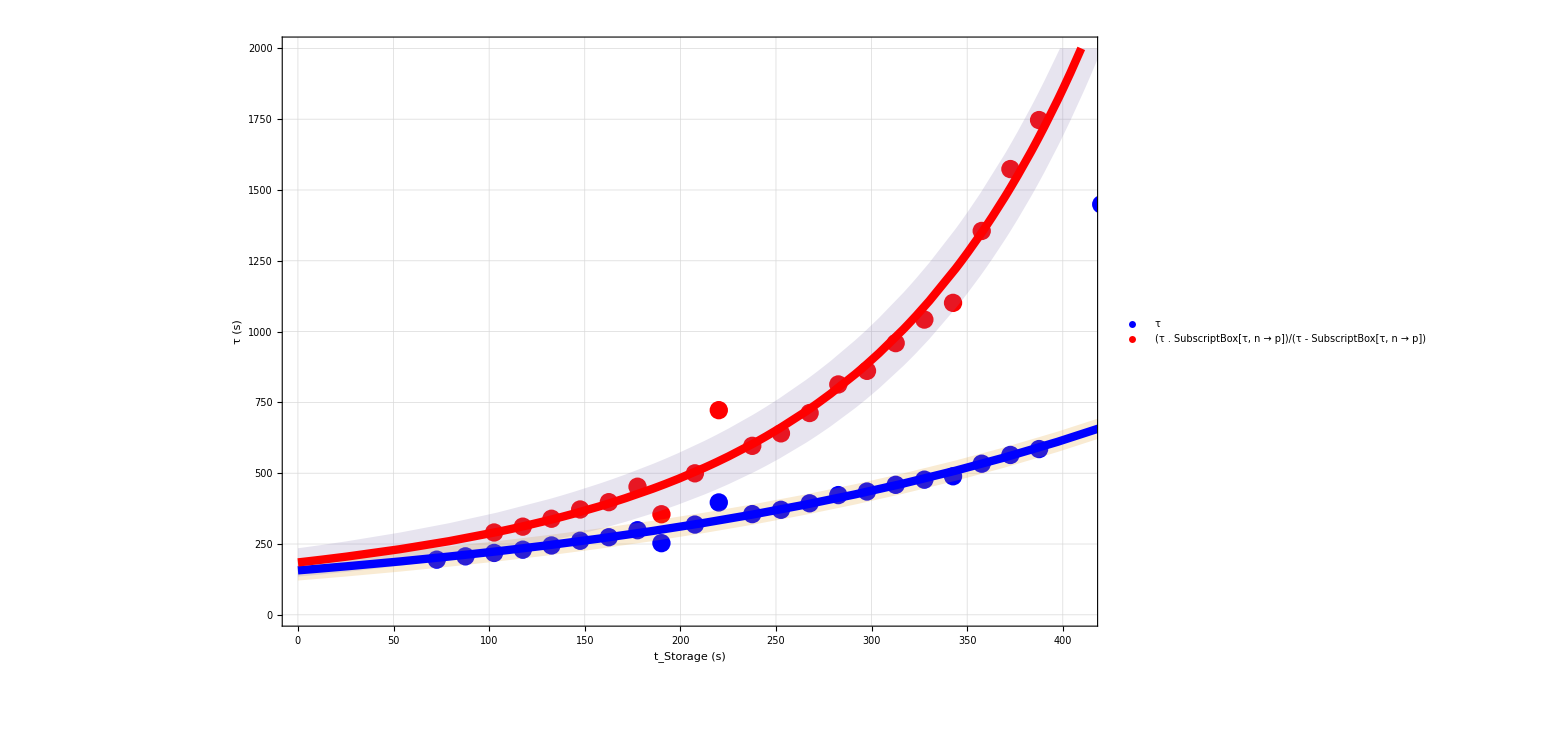

decay-halflife.png

```mathematica
Clear[shs,tabs]
tabs=3;
sttabs=tabs;
shs=Table[0,{k,1,tabs-sttabs+1}];
For[i=1,i<=tabs-sttabs+1,i++,
stnumac=i-1+sttabs;
allnumac=20;
Dimensions[finpt][[1]];
finftpt2=Table[{(finpt[[k]][[1]]+finpt[[k-stnumac+1]][[1]])/2,(finpt[[k-stnumac+1]][[1]]-finpt[[k]][[1]])/Log[finpt[[k-stnumac+1]][[2]]]/finpt[[k]][[2]]},{k,stnumac,Dimensions[finpt][[1]]}];
finftpt3=Table[{finftpt2[[k]][[1]],1/((1/finftpt2[[k]][[2]])-(1/880))},{k,stnumac,Dimensions[finftpt2][[1]]}];
(*finrealpt2=Table[{finftpt2[[k]][[1]],(finpt[[k-stnum+1]][[1]]-finpt[[k]][[1]])/Log[PlusMinus[finpt[[k-stnum+1,2]],Sqrt[Abs[finpt[[k-stnum+1,2]]]]]/PlusMinus[finpt[[k,2]],Sqrt[Abs[finpt[[k,2]]]]]][[2]]},{k,stnum,allnum+stnum}]
errallseries=Sqrt[finpt[[;;,3]]^2+(2*.397183)^2];*)
Print[nlm4=NonlinearModelFit[finftpt2[[1;;allnumac]],(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
Print["Sigmas: ",(nlm4["FitResiduals"]/errallseries[[stnumac;;]][[1;;allnumac]])];
Print["Chi^2/ndf: ",Total[((nlm4["FitResiduals"]/errallseries[[stnumac;;]][[1;;allnumac]]))^2]/(Dimensions[finpt][[1]]-2)];
Print[nlm4["ANOVATable"]];
Print[nlm4["ParameterTable"]];
Print[Grid[Transpose[{#,nlm4[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
(***)
Print[nlm42=NonlinearModelFit[finftpt3[[1;;allnumac]],{(bb Exp[t cc]+dd Exp[t ee] )},{{bb,10},{cc,-.1},{dd,10},{ee,-.1}},t,Method->NMinimize]];
Print["Sigmas: ",(nlm42["FitResiduals"]/errallseries[[stnumac;;]][[1;;allnumac]])];
Print["Chi^2/ndf: ",Total[((nlm42["FitResiduals"]/errallseries[[stnumac;;]][[1;;allnumac]]))^2]/(Dimensions[finpt][[1]]-2)];
Print[nlm42["ANOVATable"]];
Print[nlm42["ParameterTable"]];
Print[Grid[Transpose[{#,nlm42[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]];
(***)
nlm42add[xx_]:=155Exp[.003xx]+30Exp[.0095xx];
nlm42adds=100;
shs[[i]]=Show[{
EDAListPlot[finftpt2,finftpt3,PlotLegends->{"τ","(τ . SubscriptBox[τ, n → p])/(τ - SubscriptBox[τ, n → p])"},PlotRange->{{0,410},{0,2000}},GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->{Blue,Red},FrameLabel->{"t_Storage (s)","τ (s)"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->1200],
Plot[{
nlm4[xx],nlm4[xx]+4nlm4["ParameterErrors"][[1]],nlm4[xx]-4nlm4["ParameterErrors"][[1]],
nlm42add[xx],nlm42add[xx]+0.5Exp[.003xx]nlm42adds,nlm42add[xx]-0.5Exp[.003xx]nlm42adds
(*nlm42[xx],nlm42[xx]+nlm42["ParameterErrors"][[1]],nlm42[xx]-nlm42["ParameterErrors"][[1]]*)
},{xx,0,1300},Filling->{{2->{3}},{5->{6}}},PlotRange->{{0,420},{0,2000}},FillingStyle->{{Opacity[.5],Blue},{Opacity[.5],Red}},PlotStyle->{{Blue,Thickness[.005]},None,None,{Red,Thickness[.005]},None,None}]
}];
]
Show[shs]
Export["decay-halflife.png",Show[shs]]
```

## UCN Density at t=0; [(U+D/Monitor)@t=0]*(Monitor=550417)

```mathematica
mon=1050417;
t0cou=PlusMinus[(0.07816244969454503+0.05068275118657106)*mon,(0.07816244969454503+0.05068275118657106)*Sqrt[mon]]
vol=PlusMinus[(Pi*.235^2*.12*10^6),0];
Print["^UnPolN_UCN/^PolN_UCN = ",polunpolratio=PlusMinus[1.73,.08/Sqrt[7]]]
Print["^UnPolN_UCN^W1  = ",PlusMinus[22.4355,N[t0cou/(vol)][[2]]]*2000000]
Print["^PolN_UCN^DS  = ",PlusMinus[2.4482,N[t0cou/(vol*polunpolratio)][[2]]]*2000000]
Print["^UnPolN_UCN^DS  = ",PlusMinus[2.4482*polunpolratio[[1]],N[t0cou/(vol)][[2]]]*2000000]
Print["^Polρ_UCN^nEDM (cc^-1) = ",t0cou/(vol*polunpolratio)]
Print["^UnPolρ_UCN^NStar (cc^-1) = ",t0cou/vol]
```

135341.±132.053

^UnPolN_UCN/^PolN_UCN = 1.73±0.0302372

^UnPolN_UCN^W1  = 4.4871×10^7±13000.

^PolN_UCN^DS  = 4.9×10^6±130000.

^UnPolN_UCN^DS  = 8.471×10^6±13000.

^Polρ_UCN^nEDM (cc^-1) = 3.757±0.066

^UnPolρ_UCN^NStar (cc^-1) = 6.5007±0.0063